```mathematica
CompSym[s1_,s2_]:=(s1/.repColorValue)<=(s2/.repColorValue)
```

```mathematica
tri
```

{v13x24x5,v14x25x3,v1x24x35,v13x25x4,v14x2x35}

```mathematica
qua=Table[allGraphs5[k,"colofour"],{k,quads}];
```

```mathematica
FilterTri[list_]:=Block[{},Select[list,!MemberQ[qua,#]&&!MemberQ[tri,#]&]]
```

```mathematica
Select[{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x2x4x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45},!MemberQ[tri,#]&]/.repColor
```

{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x2x4x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45}

```mathematica
TableForm[Sort[Map[Sort[FilterTri[#],CompSym]&,allCrit3]]]/.repColor
```

v13x245 | v1x2x3x45 | v134x25 | v1x2x34x5 | v14x235 | v1x23x4x5 | v135x24 | v15x2x3x4 | v124x35 | v12x3x4x5
v13x245 | v1x2x3x45 | v134x25 | v1x2x34x5 | v14x235 | v1x23x4x5 | v135x24 | v15x2x3x4 | v124x3x5 | v12x35x4
v13x245 | v1x2x3x45 | v134x25 | v1x2x34x5 | v14x235 | v1x23x4x5 | v135x2x4 | v15x24x3 | v124x35 | v12x3x4x5
v13x245 | v1x2x3x45 | v134x25 | v1x2x34x5 | v14x235 | v1x23x4x5 | v135x2x4 | v15x24x3 | v124x3x5 | v12x35x4
v13x245 | v1x2x3x45 | v134x25 | v1x2x34x5 | v14x23x5 | v1x235x4 | v135x24 | v15x2x3x4 | v124x35 | v12x3x4x5
v13x245 | v1x2x3x45 | v134x25 | v1x2x34x5 | v14x23x5 | v1x235x4 | v135x24 | v15x2x3x4 | v124x3x5 | v12x35x4
v13x245 | v1x2x3x45 | v134x25 | v1x2x34x5 | v14x23x5 | v1x235x4 | v135x2x4 | v15x24x3 | v124x35 | v12x3x4x5
v13x245 | v1x2x3x45 | v134x25 | v1x2x34x5 | v14x23x5 | v1x235x4 | v135x2x4 | v15x24x3 | v124x3x5 | v12x35x4
v13x245 | v1x2x3x45 | v134x2x5 | v1x25x34 | v14x235 | v1x23x4x5 | v135x24 | v15x2x3x4 | v124x35 | v12x3x4x5
v13x245 | v1x2x3x45 | v134x2x5 | v1x25x34 | v14x235 | v1x23x4x5 | v135x24 | v15x2x3x4 | v124x3x5 | v12x35x4
v13x245 | v1x2x3x45 | v134x2x5 | v1x25x34 | v14x235 | v1x23x4x5 | v135x2x4 | v15x24x3 | v124x35 | v12x3x4x5
v13x245 | v1x2x3x45 | v134x2x5 | v1x25x34 | v14x235 | v1x23x4x5 | v135x2x4 | v15x24x3 | v124x3x5 | v12x35x4
v13x245 | v1x2x3x45 | v134x2x5 | v1x25x34 | v14x23x5 | v1x235x4 | v135x24 | v15x2x3x4 | v124x35 | v12x3x4x5
v13x245 | v1x2x3x45 | v134x2x5 | v1x25x34 | v14x23x5 | v1x235x4 | v135x24 | v15x2x3x4 | v124x3x5 | v12x35x4
v13x245 | v1x2x3x45 | v134x2x5 | v1x25x34 | v14x23x5 | v1x235x4 | v135x2x4 | v15x24x3 | v124x35 | v12x3x4x5
v13x245 | v1x2x3x45 | v134x2x5 | v1x25x34 | v14x23x5 | v1x235x4 | v135x2x4 | v15x24x3 | v124x3x5 | v12x35x4
v13x2x45 | v1x245x3 | v134x25 | v1x2x34x5 | v14x235 | v1x23x4x5 | v135x24 | v15x2x3x4 | v124x35 | v12x3x4x5
v13x2x45 | v1x245x3 | v134x25 | v1x2x34x5 | v14x235 | v1x23x4x5 | v135x24 | v15x2x3x4 | v124x3x5 | v12x35x4
v13x2x45 | v1x245x3 | v134x25 | v1x2x34x5 | v14x235 | v1x23x4x5 | v135x2x4 | v15x24x3 | v124x35 | v12x3x4x5
v13x2x45 | v1x245x3 | v134x25 | v1x2x34x5 | v14x235 | v1x23x4x5 | v135x2x4 | v15x24x3 | v124x3x5 | v12x35x4
v13x2x45 | v1x245x3 | v134x25 | v1x2x34x5 | v14x23x5 | v1x235x4 | v135x24 | v15x2x3x4 | v124x35 | v12x3x4x5
v13x2x45 | v1x245x3 | v134x25 | v1x2x34x5 | v14x23x5 | v1x235x4 | v135x24 | v15x2x3x4 | v124x3x5 | v12x35x4
v13x2x45 | v1x245x3 | v134x25 | v1x2x34x5 | v14x23x5 | v1x235x4 | v135x2x4 | v15x24x3 | v124x35 | v12x3x4x5
v13x2x45 | v1x245x3 | v134x25 | v1x2x34x5 | v14x23x5 | v1x235x4 | v135x2x4 | v15x24x3 | v124x3x5 | v12x35x4
v13x2x45 | v1x245x3 | v134x2x5 | v1x25x34 | v14x235 | v1x23x4x5 | v135x24 | v15x2x3x4 | v124x35 | v12x3x4x5
v13x2x45 | v1x245x3 | v134x2x5 | v1x25x34 | v14x235 | v1x23x4x5 | v135x24 | v15x2x3x4 | v124x3x5 | v12x35x4
v13x2x45 | v1x245x3 | v134x2x5 | v1x25x34 | v14x235 | v1x23x4x5 | v135x2x4 | v15x24x3 | v124x35 | v12x3x4x5
v13x2x45 | v1x245x3 | v134x2x5 | v1x25x34 | v14x235 | v1x23x4x5 | v135x2x4 | v15x24x3 | v124x3x5 | v12x35x4
v13x2x45 | v1x245x3 | v134x2x5 | v1x25x34 | v14x23x5 | v1x235x4 | v135x24 | v15x2x3x4 | v124x35 | v12x3x4x5
v13x2x45 | v1x245x3 | v134x2x5 | v1x25x34 | v14x23x5 | v1x235x4 | v135x24 | v15x2x3x4 | v124x3x5 | v12x35x4
v13x2x45 | v1x245x3 | v134x2x5 | v1x25x34 | v14x23x5 | v1x235x4 | v135x2x4 | v15x24x3 | v124x35 | v12x3x4x5
v13x2x45 | v1x245x3 | v134x2x5 | v1x25x34 | v14x23x5 | v1x235x4 | v135x2x4 | v15x24x3 | v124x3x5 | v12x35x4

```mathematica
TableForm[DeleteDuplicates[Sort[Map[Sort[FilterTri[#],CompSym]&,Map[ListofVars,ExpressionToList[allCrit]]]]]]/.repColor
```

v13x245 | v1x2x3x45 | v134x25 | v1x2x34x5 | v14x235 | v1x23x4x5 | v135x24 | v15x2x3x4 | v124x35 | v12x3x4x5
v13x245 | v1x2x3x45 | v134x25 | v1x2x34x5 | v14x235 | v1x23x4x5 | v135x24 | v15x2x3x4 | v124x3x5 | v12x35x4
v13x245 | v1x2x3x45 | v134x25 | v1x2x34x5 | v14x235 | v1x23x4x5 | v135x2x4 | v15x24x3 | v124x35 | v12x3x4x5
v13x245 | v1x2x3x45 | v134x25 | v1x2x34x5 | v14x235 | v1x23x4x5 | v135x2x4 | v15x24x3 | v124x3x5 | v12x35x4
v13x245 | v1x2x3x45 | v134x25 | v1x2x34x5 | v14x23x5 | v1x235x4 | v135x24 | v15x2x3x4 | v124x35 | v12x3x4x5
v13x245 | v1x2x3x45 | v134x25 | v1x2x34x5 | v14x23x5 | v1x235x4 | v135x24 | v15x2x3x4 | v124x3x5 | v12x35x4
v13x245 | v1x2x3x45 | v134x25 | v1x2x34x5 | v14x23x5 | v1x235x4 | v135x2x4 | v15x24x3 | v124x35 | v12x3x4x5
v13x245 | v1x2x3x45 | v134x25 | v1x2x34x5 | v14x23x5 | v1x235x4 | v135x2x4 | v15x24x3 | v124x3x5 | v12x35x4
v13x245 | v1x2x3x45 | v134x2x5 | v1x25x34 | v14x235 | v1x23x4x5 | v135x24 | v15x2x3x4 | v124x35 | v12x3x4x5
v13x245 | v1x2x3x45 | v134x2x5 | v1x25x34 | v14x235 | v1x23x4x5 | v135x24 | v15x2x3x4 | v124x3x5 | v12x35x4
v13x245 | v1x2x3x45 | v134x2x5 | v1x25x34 | v14x235 | v1x23x4x5 | v135x2x4 | v15x24x3 | v124x35 | v12x3x4x5
v13x245 | v1x2x3x45 | v134x2x5 | v1x25x34 | v14x235 | v1x23x4x5 | v135x2x4 | v15x24x3 | v124x3x5 | v12x35x4
v13x245 | v1x2x3x45 | v134x2x5 | v1x25x34 | v14x23x5 | v1x235x4 | v135x24 | v15x2x3x4 | v124x35 | v12x3x4x5
v13x245 | v1x2x3x45 | v134x2x5 | v1x25x34 | v14x23x5 | v1x235x4 | v135x24 | v15x2x3x4 | v124x3x5 | v12x35x4
v13x245 | v1x2x3x45 | v134x2x5 | v1x25x34 | v14x23x5 | v1x235x4 | v135x2x4 | v15x24x3 | v124x35 | v12x3x4x5
v13x245 | v1x2x3x45 | v134x2x5 | v1x25x34 | v14x23x5 | v1x235x4 | v135x2x4 | v15x24x3 | v124x3x5 | v12x35x4
v13x2x45 | v1x245x3 | v134x25 | v1x2x34x5 | v14x235 | v1x23x4x5 | v135x24 | v15x2x3x4 | v124x35 | v12x3x4x5
v13x2x45 | v1x245x3 | v134x25 | v1x2x34x5 | v14x235 | v1x23x4x5 | v135x24 | v15x2x3x4 | v124x3x5 | v12x35x4
v13x2x45 | v1x245x3 | v134x25 | v1x2x34x5 | v14x235 | v1x23x4x5 | v135x2x4 | v15x24x3 | v124x35 | v12x3x4x5
v13x2x45 | v1x245x3 | v134x25 | v1x2x34x5 | v14x235 | v1x23x4x5 | v135x2x4 | v15x24x3 | v124x3x5 | v12x35x4
v13x2x45 | v1x245x3 | v134x25 | v1x2x34x5 | v14x23x5 | v1x235x4 | v135x24 | v15x2x3x4 | v124x35 | v12x3x4x5
v13x2x45 | v1x245x3 | v134x25 | v1x2x34x5 | v14x23x5 | v1x235x4 | v135x24 | v15x2x3x4 | v124x3x5 | v12x35x4
v13x2x45 | v1x245x3 | v134x25 | v1x2x34x5 | v14x23x5 | v1x235x4 | v135x2x4 | v15x24x3 | v124x35 | v12x3x4x5
v13x2x45 | v1x245x3 | v134x25 | v1x2x34x5 | v14x23x5 | v1x235x4 | v135x2x4 | v15x24x3 | v124x3x5 | v12x35x4
v13x2x45 | v1x245x3 | v134x2x5 | v1x25x34 | v14x235 | v1x23x4x5 | v135x24 | v15x2x3x4 | v124x35 | v12x3x4x5
v13x2x45 | v1x245x3 | v134x2x5 | v1x25x34 | v14x235 | v1x23x4x5 | v135x24 | v15x2x3x4 | v124x3x5 | v12x35x4
v13x2x45 | v1x245x3 | v134x2x5 | v1x25x34 | v14x235 | v1x23x4x5 | v135x2x4 | v15x24x3 | v124x35 | v12x3x4x5
v13x2x45 | v1x245x3 | v134x2x5 | v1x25x34 | v14x235 | v1x23x4x5 | v135x2x4 | v15x24x3 | v124x3x5 | v12x35x4
v13x2x45 | v1x245x3 | v134x2x5 | v1x25x34 | v14x23x5 | v1x235x4 | v135x24 | v15x2x3x4 | v124x35 | v12x3x4x5
v13x2x45 | v1x245x3 | v134x2x5 | v1x25x34 | v14x23x5 | v1x235x4 | v135x24 | v15x2x3x4 | v124x3x5 | v12x35x4
v13x2x45 | v1x245x3 | v134x2x5 | v1x25x34 | v14x23x5 | v1x235x4 | v135x2x4 | v15x24x3 | v124x35 | v12x3x4x5
v13x2x45 | v1x245x3 | v134x2x5 | v1x25x34 | v14x23x5 | v1x235x4 | v135x2x4 | v15x24x3 | v124x3x5 | v12x35x4

```mathematica
Select[Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}],!MemberQ[qua,#]&&!MemberQ[tri,#]&&allGraphs5[#/.RepKey["C"],"comp"]=!=GreaterEqual&]/.RepGraph["C"]
```

{-Graphics-295240,-Graphics-295371,-Graphics-297681,-Graphics-298571,-Graphics-298881,-Graphics-302621,-Graphics-304961,-Graphics-305861,-Graphics-324411,-Graphics-326841,-Graphics-390141,-Graphics-492081,-Graphics-492161,-Graphics-492201,-Graphics-499631,-Graphics-499721,-Graphics-522321,-Graphics-560111,-Graphics-560121,-Graphics-567701,-Graphics-582881,-Graphics-590481}

```mathematica
Select[Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}],!MemberQ[qua,#]&&!MemberQ[tri,#]&&allGraphs5[#/.RepKey["C"],"comp"]===GreaterEqual&]//Length
```

20

## and here

```mathematica
buddies=Block[{
sols=Association[],
todo=ZeVars8,
i,
current,
buddy,
antibuddy,
range=Map[ListofVars,ExpressionToList[allCrit]],
qua=Table[allGraphs5[k,"colofour"],{k,quads}]
},
todo=Select[todo,!MemberQ[qua,#]&];
For[i=1,Length[todo]≠0,i++,
current=todo[[1]];
buddy=Join[{current},Buddy[current,range]];
antibuddy=Join[AntiBuddy[current,range]];
sols[i]={};
Table[AppendTo[sols[i],b],{b,buddy}];
(*Table[AppendTo[sols[i],b],{b,antibuddy}];*)
todo=Select[todo,!MemberQ[buddy,#]&&!MemberQ[antibuddy,#]&];
];
Select[Values[sols],Length[#]≠1&]
]
```

{{v1x2x3x45,v13x245},{v1x2x34x5,v134x25},{v1x23x4x5,v14x235},{v15x2x3x4,v135x24},{v12x3x4x5,v124x35}}

```mathematica
Join[quads,(Flatten[buddies]/.RepKey["C"])]
```

{36085,29605,29527,31711,29551,29525,36194,29533,38308,29767,31984,30253,36898,49207,51478}

```mathematica
Table[allGraphs5[k,"comp"]=Greater;allGraphs5[k,"compwhy"]="buddies cannot be zero at the same time";
allGraphs5[k,"atleast"]=1;allGraphs5[k,"atleastwhy"]="buddies cannot be zero at the same time",{k,Join[quads,(Flatten[buddies]/.RepKey["C"])]}]
```

{buddies cannot be zero at the same time,buddies cannot be zero at the same time,buddies cannot be zero at the same time,buddies cannot be zero at the same time,buddies cannot be zero at the same time,buddies cannot be zero at the same time,buddies cannot be zero at the same time,buddies cannot be zero at the same time,buddies cannot be zero at the same time,buddies cannot be zero at the same time,buddies cannot be zero at the same time,buddies cannot be zero at the same time,buddies cannot be zero at the same time,buddies cannot be zero at the same time,buddies cannot be zero at the same time}

```mathematica
PropagateAtLeast[];
```

```mathematica
PropagateAtLeast[]
```

{280,{0,0,19683,19683,26244,26244,28431,28431,29160,29160,29403,29403,29484,29484,29511,29511,29520,29493,29574,29430,29439,29412,29241,29268,29277,29250,29322,29187,29196,29169,28674,28755,28782,28791,28764,28845,28701,28710,28683,28512,28539,28548,28521,28593,28458,28467,28440,26973,27216,27297,27324,27333,27306,27243,27252,27225,27054,27081,27090,27063,27000,27009,26982,26487,26568,26595,26604,26577,26514,26523,26496,26325,26352,26361,26334,26271,26280,26253,36057,35325,33861,33129,21870,22599,22842,22923,22950,22959,22932,22869,22878,22851,22680,22707,22716,22689,22626,22635,22608,22113,22194,22221,22230,22203,22140,22149,22122,21951,21978,21987,21960,21897,21906,21879,20412,20655,20736,20763,20772,20745,20682,20691,20664,20493,20520,20529,20502,20439,20448,20421,19926,20007,20034,20043,20016,19953,19962,19935,19764,19791,19800,19773,19710,19719,19692,6561,8748,9477,9720,9801,9828,9837,9810,9747,9756,9729,9558,9585,9594,9567,9504,9513,9486,8991,9072,9099,9108,9081,9018,9027,9000,8829,8856,8865,8838,8775,8784,8757,7290,7533,7614,7641,7650,7623,7704,7560,7569,7542,7371,7398,7407,7380,7452,7317,7326,7299,6804,6885,6912,6921,6894,6975,6831,6840,6813,6642,6669,6678,6651,6723,6588,6597,6570,16131,15399,13935,13203,2187,2916,3159,3240,3267,3276,3249,3186,3195,3168,2997,3024,3033,3006,2943,2952,2925,2430,2511,2538,2547,2520,2457,2466,2439,2268,2295,2304,2277,2214,2223,2196,729,972,1053,1080,1089,1062,999,1008,981,810,837,846,819,756,765,738,243,324,351,360,333,270,279,252,81,108,117,90,27,36,9}}

```mathematica
PropagateAtLeast[]
```

{0,{}}

```mathematica
PropagateComp[]
```

0

```mathematica
PropagateAtLeast[]
```

{0,{}}

```mathematica
PropagateComp[]:=Block[{leftKey,rightKey,left,right,current,changed=0},
Monitor[
Table[
current = allGraphs5[k];
Table[
leftKey=children[[1]];
rightKey=children[[2]];
left=allGraphs5[leftKey];
right=allGraphs5[rightKey];
If[current["comp"]===GreaterEqual && (left["comp"]===Greater),
current["compwhy"]="The relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (greater propagated from left)";
current["comp"]=Greater;
Print[current["compwhy"]];
changed++;
allGraphs5[k]=current;
];

If[current["comp"]===GreaterEqual && (right["comp"]===Greater),
current["compwhy"]="The relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (greater propagated from right)";
current["comp"]=Greater;
Print[current["compwhy"]];
changed++;
allGraphs5[k]=current;
];

If[current["comp"]===GreaterEqual && (left["comp"]===Equal&&right["comp"]===Equal),
current["compwhy"]="The relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (zero propagated)";
current["comp"]=Equal;
Print[current["compwhy"]];
changed++;
allGraphs5[k]=current;
];
If[current["comp"]===GreaterEqual && (left["comp"]===Equal&&right["comp"]===Greater),
current["compwhy"]="The relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (Greater (right) and zero (left) propagated)";
current["comp"]=Greater;
Print[current["compwhy"]];
changed++;
allGraphs5[k]=current;
];

If[current["comp"]===GreaterEqual && (left["comp"]===Greater&&right["comp"]===Equal),
current["compwhy"]="The relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (Zero (right) and Greater (left) propagated)";
current["comp"]=Greater;
Print[current["compwhy"]];
changed++;
allGraphs5[k]=current;
];

If[current["comp"]===Greater && (left["comp"]===GreaterEqual&&right["comp"]===Equal),
left["compwhy"]="The down relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (Greater(parent) and zero(right) pushed down to left)";
left["comp"]=Greater;
Print[left["compwhy"]];
changed++;
allGraphs5[children[[1]]]=left;
];

If[current["comp"]===Greater && (left["comp"]===Equal&&right["comp"]===GreaterEqual),
right["compwhy"]="The down relation holds "<> ToString[k]<> "("<> ToString[current["comp"]]<> ") == "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> " (" <>ToString[right["comp"]]<>") (Greater(parent) and zero(left) pushed down to right)";
right["comp"]=Greater;
Print[right["compwhy"]];
changed++;
allGraphs5[children[[2]]]=right;
]
,{children,allGraphs5[k,"children"]}
]
,
{k,Keys[allGraphs5]}],
k
];
changed
]
```

```mathematica
PropagateComp[]
```

The relation holds 29520(GreaterEqual)== 29521(GreaterEqual) + 29525 (Greater) (greater propagated from right)

The relation holds 29523(GreaterEqual)== 29524(Equal) + 29525 (Greater) (greater propagated from right)

The relation holds 29514(GreaterEqual)== 29523(Greater) + 29533 (Greater) (greater propagated from left)

The relation holds 29515(GreaterEqual)== 29524(Equal) + 29533 (Greater) (greater propagated from right)

The relation holds 29512(GreaterEqual)== 29521(GreaterEqual) + 29533 (Greater) (greater propagated from right)

The relation holds 29493(GreaterEqual)== 29520(Greater) + 29551 (GreaterEqual) (greater propagated from left)

The relation holds 29496(GreaterEqual)== 29523(Greater) + 29551 (GreaterEqual) (greater propagated from left)

The relation holds 29439(GreaterEqual)== 29520(Greater) + 29602 (GreaterEqual) (greater propagated from left)

The relation holds 29442(GreaterEqual)== 29523(Greater) + 29605 (GreaterEqual) (greater propagated from left)

The relation holds 29433(GreaterEqual)== 29514(Greater) + 29605 (GreaterEqual) (greater propagated from left)

The relation holds 29434(GreaterEqual)== 29515(Greater) + 29605 (GreaterEqual) (greater propagated from left)

The relation holds 29431(GreaterEqual)== 29512(Greater) + 29602 (GreaterEqual) (greater propagated from left)

The relation holds 29281(GreaterEqual)== 29524(Equal) + 29767 (Greater) (greater propagated from right)

The relation holds 29278(GreaterEqual)== 29521(GreaterEqual) + 29767 (Greater) (greater propagated from right)

The relation holds 29272(GreaterEqual)== 29515(Greater) + 29767 (Greater) (greater propagated from left)

The relation holds 29269(GreaterEqual)== 29512(Greater) + 29767 (Greater) (greater propagated from left)

The relation holds 29254(GreaterEqual)== 29497(GreaterEqual) + 29767 (Greater) (greater propagated from right)

The relation holds 29200(GreaterEqual)== 29443(GreaterEqual) + 29767 (Greater) (greater propagated from right)

The relation holds 29197(GreaterEqual)== 29440(GreaterEqual) + 29767 (Greater) (greater propagated from right)

The relation holds 29173(GreaterEqual)== 29416(GreaterEqual) + 29767 (Greater) (greater propagated from right)

The relation holds 28791(GreaterEqual)== 29520(Greater) + 30253 (Greater) (greater propagated from left)

The relation holds 28794(GreaterEqual)== 29523(Greater) + 30253 (Greater) (greater propagated from left)

The relation holds 28795(GreaterEqual)== 29524(Equal) + 30253 (Greater) (greater propagated from right)

The relation holds 28792(GreaterEqual)== 29521(GreaterEqual) + 30253 (Greater) (greater propagated from right)

The relation holds 28764(GreaterEqual)== 29493(Greater) + 30253 (Greater) (greater propagated from left)

The relation holds 28767(GreaterEqual)== 29496(Greater) + 30253 (Greater) (greater propagated from left)

The relation holds 28768(GreaterEqual)== 29497(GreaterEqual) + 30253 (Greater) (greater propagated from right)

The relation holds 28765(GreaterEqual)== 29494(GreaterEqual) + 30253 (Greater) (greater propagated from right)

The relation holds 31492(GreaterEqual)== 31738(GreaterEqual) + 31984 (Greater) (greater propagated from right)

The relation holds 31444(GreaterEqual)== 31714(GreaterEqual) + 31984 (Greater) (greater propagated from right)

The relation holds 27333(GreaterEqual)== 29520(Greater) + 31708 (GreaterEqual) (greater propagated from left)

The relation holds 27336(GreaterEqual)== 29523(Greater) + 31711 (GreaterEqual) (greater propagated from left)

The relation holds 27327(GreaterEqual)== 29514(Greater) + 31711 (GreaterEqual) (greater propagated from left)

The relation holds 27328(GreaterEqual)== 29515(Greater) + 31711 (GreaterEqual) (greater propagated from left)

The relation holds 27325(GreaterEqual)== 29512(Greater) + 31708 (GreaterEqual) (greater propagated from left)

The relation holds 27309(GreaterEqual)== 29496(Greater) + 31684 (GreaterEqual) (greater propagated from left)

The relation holds 27255(GreaterEqual)== 29442(Greater) + 31711 (GreaterEqual) (greater propagated from left)

The relation holds 27246(GreaterEqual)== 29433(Greater) + 31711 (GreaterEqual) (greater propagated from left)

The relation holds 27247(GreaterEqual)== 29434(Greater) + 31711 (GreaterEqual) (greater propagated from left)

The relation holds 26608(GreaterEqual)== 28795(Greater) + 31711 (GreaterEqual) (greater propagated from left)

The relation holds 26605(GreaterEqual)== 28792(Greater) + 31708 (GreaterEqual) (greater propagated from left)

The relation holds 26581(GreaterEqual)== 28768(Greater) + 31684 (GreaterEqual) (greater propagated from left)

The relation holds 36138(GreaterEqual)== 36166(GreaterEqual) + 36194 (Greater) (greater propagated from right)

The relation holds 36030(GreaterEqual)== 36112(GreaterEqual) + 36194 (Greater) (greater propagated from right)

The relation holds 35406(GreaterEqual)== 36138(Greater) + 36898 (Greater) (greater propagated from left)

The relation holds 35434(GreaterEqual)== 36166(GreaterEqual) + 36898 (Greater) (greater propagated from right)

The relation holds 33916(GreaterEqual)== 36112(GreaterEqual) + 38308 (Greater) (greater propagated from right)

The relation holds 33834(GreaterEqual)== 36030(Greater) + 38308 (Greater) (greater propagated from left)

The relation holds 22954(GreaterEqual)== 29515(Greater) + 36085 (GreaterEqual) (greater propagated from left)

The relation holds 22951(GreaterEqual)== 29512(Greater) + 36085 (GreaterEqual) (greater propagated from left)

The relation holds 22873(GreaterEqual)== 29434(Greater) + 36004 (GreaterEqual) (greater propagated from left)

The relation holds 22720(GreaterEqual)== 29281(Greater) + 36085 (GreaterEqual) (greater propagated from left)

The relation holds 22717(GreaterEqual)== 29278(Greater) + 36085 (GreaterEqual) (greater propagated from left)

The relation holds 22711(GreaterEqual)== 29272(Greater) + 36085 (GreaterEqual) (greater propagated from left)

The relation holds 22708(GreaterEqual)== 29269(Greater) + 36085 (GreaterEqual) (greater propagated from left)

The relation holds 22693(GreaterEqual)== 29254(Greater) + 36058 (GreaterEqual) (greater propagated from left)

The relation holds 22639(GreaterEqual)== 29200(Greater) + 36004 (GreaterEqual) (greater propagated from left)

The relation holds 22234(GreaterEqual)== 28795(Greater) + 36085 (GreaterEqual) (greater propagated from left)

The relation holds 22207(GreaterEqual)== 28768(Greater) + 36058 (GreaterEqual) (greater propagated from left)

The relation holds 22318(GreaterEqual)== 29608(GreaterEqual) + 36898 (Greater) (greater propagated from right)

The relation holds 25168(GreaterEqual)== 31738(GreaterEqual) + 38308 (Greater) (greater propagated from right)

The relation holds 24922(GreaterEqual)== 31492(Greater) + 38308 (Greater) (greater propagated from left)

The relation holds 20047(GreaterEqual)== 26608(Greater) + 36085 (GreaterEqual) (greater propagated from left)

The relation holds 9841(GreaterEqual)== 29524(Equal) + 49207 (Greater) (greater propagated from right)

The relation holds 9814(GreaterEqual)== 29497(GreaterEqual) + 49207 (Greater) (greater propagated from right)

The relation holds 9760(GreaterEqual)== 29443(GreaterEqual) + 49207 (Greater) (greater propagated from right)

The relation holds 9733(GreaterEqual)== 29416(GreaterEqual) + 49207 (Greater) (greater propagated from right)

The relation holds 9598(GreaterEqual)== 29281(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 9571(GreaterEqual)== 29254(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 9517(GreaterEqual)== 29200(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 9490(GreaterEqual)== 29173(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 9112(GreaterEqual)== 28795(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 11950(GreaterEqual)== 31714(GreaterEqual) + 51478 (Greater) (greater propagated from right)

The relation holds 11680(GreaterEqual)== 31444(Greater) + 51478 (Greater) (greater propagated from left)

The relation holds 7654(GreaterEqual)== 27337(GreaterEqual) + 49207 (Greater) (greater propagated from right)

The relation holds 7627(GreaterEqual)== 27310(GreaterEqual) + 49207 (Greater) (greater propagated from right)

The relation holds 7738(GreaterEqual)== 29608(GreaterEqual) + 51478 (Greater) (greater propagated from right)

The relation holds 6925(GreaterEqual)== 26608(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 3280(GreaterEqual)== 22963(GreaterEqual) + 49207 (Greater) (greater propagated from right)

The relation holds 3253(GreaterEqual)== 22936(GreaterEqual) + 49207 (Greater) (greater propagated from right)

The relation holds 3199(GreaterEqual)== 22882(GreaterEqual) + 49207 (Greater) (greater propagated from right)

The relation holds 2551(GreaterEqual)== 22234(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 1093(GreaterEqual)== 20776(GreaterEqual) + 49207 (Greater) (greater propagated from right)

The relation holds 364(GreaterEqual)== 20047(Greater) + 49207 (Greater) (greater propagated from left)

The relation holds 448(GreaterEqual)== 22318(Greater) + 51478 (Greater) (greater propagated from left)

85

```mathematica
PropagateComp[]
```

0

```mathematica
Clear[RepGraph];RepGraph[base_]:=RepGraph[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->ShowGraph5Least[key],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepZero];RepZero[base_]:=RepZero[base]=Table[With[{var=allGraphs5[k,Bases[base,"Colofour"]]},var->If[allGraphs5[k,"comp"]===Equal,0,var]],{k,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepKey];RepKey[base_]:=RepKey[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->key,{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepAtLeast];RepAtLeast[base_]:=RepAtLeast[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->allGraphs5[key,"atleast"],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepEmbed];RepEmbed[base_]:=RepEmbed[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->allGraphs5[key,"embed"],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepChromial];RepChromial[base_]:=RepChromial[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->ChromaticPolynomial[allGraphs5[key,"graph"],x],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepBase];RepBase[base_,base2_]:=RepBase[base,base2]=Table[allGraphs5[key,Bases[base,"Colofour"]]->allGraphs5[key,Bases[base2,"Colofour"]],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
With[
{base="C",colofour="colofour"},
Select[Keys[allGraphs5],(allGraphs5[#,"atleast"]≠ (allGraphs5[#,colofour]/.RepAtLeast[base]))&]
]
```

{}

```mathematica
allCrit666=With[
{base="C",colofour="colofour"},
Fold[And,
Map[Fold[Or,Table[var>(var/.RepAtLeast[base]),{var,ListofVars[(allGraphs5[#,colofour]/.RepZero[base])]}]]&,
Select[Keys[allGraphs5],(allGraphs5[#,"atleast"]≠ (allGraphs5[#,colofour]/.RepAtLeast[base]))&]
]
]
];
```

```mathematica
Table[ShowGraph5Least[k],{k,allGraphs5AtomKeys}]
```

{-Graphics-295240,-Graphics-295251,-Graphics-295271,-Graphics-295331,-Graphics-295371,-Graphics-295511,-Graphics-295600,-Graphics-296051,-Graphics-296080,-Graphics-296330,-Graphics-297671,-Graphics-297681,-Graphics-297970,-Graphics-298571,-Graphics-298881,-Graphics-302531,-Graphics-302621,-Graphics-303340,-Graphics-304961,-Graphics-305861,-Graphics-317111,-Graphics-317140,-Graphics-317380,-Graphics-319540,-Graphics-319841,-Graphics-324411,-Graphics-326841,-Graphics-360851,-Graphics-360860,-Graphics-361120,-Graphics-361660,-Graphics-361941,-Graphics-368170,-Graphics-368981,-Graphics-382810,-Graphics-383081,-Graphics-390141,-Graphics-492071,-Graphics-492081,-Graphics-492100,-Graphics-492161,-Graphics-492201,-Graphics-499631,-Graphics-499721,-Graphics-514750,-Graphics-514781,-Graphics-522321,-Graphics-560111,-Graphics-560121,-Graphics-567701,-Graphics-582881,-Graphics-590481}

```mathematica
Table[{k,(allGraphs5[k,"atleast"]), (allGraphs5[k,"colofour"]/.RepAtLeast["C"]),(allGraphs5[k,"colofourrealnull"]/.RepAtLeast["E"])},{k,Keys[allGraphs5]}]
```

{{0,36,36,36},{19683,23,23,23},{26244,18,18,18},{28431,14,14,14},{29160,10,10,10},{29403,6,6,6},{29484,5,5,5},{29511,4,4,4},{29520,2,2,2},{29523,1,1,1},{29524,0,0,0},{29525,1,1,1},{29527,1,1,1},{29521,1,1,1},{29529,2,2,2},{29533,1,1,1},{29537,1,1,1},{29514,2,2,2},{29515,1,1,1},{29517,2,2,2},{29512,2,2,2},{29513,2,2,2},{29542,1,1,1},{29551,1,1,1},{29560,0,0,0},{29493,3,3,3},1843,{36,17,17,17},{39,14,14,14},{40,8,8,8},{37,11,11,11},{45,9,9,9},{49,6,6,6},{30,20,20,20},{31,14,14,14},{28,17,17,17},{54,10,10,10},{63,6,6,6},{72,4,4,4},{9,23,23,23},{12,18,18,18},{13,10,10,10},{14,8,8,8},{16,5,5,5},{10,15,15,15},{18,13,13,13},{22,8,8,8},{26,5,5,5},{3,26,26,26},{4,18,18,18},{6,10,10,10},{1,23,23,23},{2,13,13,13}}
 |  |  |  |

```mathematica
Map[Last,Table[{(allGraphs5[k,"atleast"]), (allGraphs5[k,"colofour"]/.RepAtLeast["C"]),(allGraphs5[k,"colofourrealnull"]/.RepAtLeast["E"])},{k,Keys[allGraphs5]}]//Tally//Sort]
```

{16,176,280,245,230,186,200,100,110,70,71,45,40,25,30,15,10,15,10,10,5,5,1}

```mathematica
Table[ ShowGraph5Least[k],{k, Select[Keys[allGraphs5],allGraphs5[#,"atleast"]≥18&]}]
```

{-Graphics-036,-Graphics-1968323,-Graphics-2624418,-Graphics-1971018,-Graphics-656126,-Graphics-874820,-Graphics-680418,-Graphics-664220,-Graphics-658820,-Graphics-656420,-Graphics-218726,-Graphics-291618,-Graphics-226820,-Graphics-221420,-Graphics-219020,-Graphics-218818,-Graphics-72923,-Graphics-75618,-Graphics-24323,-Graphics-32418,-Graphics-8126,-Graphics-10820,-Graphics-9018,-Graphics-8420,-Graphics-2726,-Graphics-3020,-Graphics-923,-Graphics-1218,-Graphics-326,-Graphics-418,-Graphics-123}

```mathematica
allGraphs5[0,"colofour"]/.RepGraph["C"]
```

-Graphics-590481+-Graphics-582881+-Graphics-567701+-Graphics-560121+-Graphics-522321+-Graphics-499721+-Graphics-492201+-Graphics-514781+-Graphics-390141+-Graphics-326841+-Graphics-305861+-Graphics-298881+-Graphics-319841+-Graphics-368981+-Graphics-361941+-Graphics-383081+-Graphics-560111+-Graphics-514750+-Graphics-492161+-Graphics-499631+-Graphics-492100+-Graphics-492081+-Graphics-382810+-Graphics-319540+-Graphics-298571+-Graphics-361660+-Graphics-368170+-Graphics-304961+-Graphics-297970+-Graphics-361120+-Graphics-360860+-Graphics-297681+-Graphics-324411+-Graphics-303340+-Graphics-296330+-Graphics-317380+-Graphics-302621+-Graphics-295600+-Graphics-295371+-Graphics-317140+-Graphics-296080+-Graphics-492071+-Graphics-360851+-Graphics-297671+-Graphics-317111+-Graphics-296051+-Graphics-295331+-Graphics-302531+-Graphics-295511+-Graphics-295251+-Graphics-295271+-Graphics-295240

```mathematica
Put[allCrit666,"d:\\Saved\\longway3.m"]
```

```mathematica
Length[allCrit666]
```

2

```mathematica
allCrit666
```

Fold[And,{}]

```mathematica
allCrit667=Reduce[allCrit666];
```

```mathematica
Length[allCrit667]
```

17

```mathematica
(ExpressionToList[allCrit667]//TableForm)/.RepGraph["C"]
```

-Graphics-317380>0&&-Graphics-317140>0&&-Graphics-361120>0&&-Graphics-296080>0&&-Graphics-361660>0
-Graphics-317110>0&&-Graphics-361120>0&&-Graphics-295270>0&&-Graphics-361660>0
-Graphics-317380>0&&-Graphics-295270>0&&-Graphics-361660>0
-Graphics-317140>0&&-Graphics-295510>0&&-Graphics-361660>0
-Graphics-296080>0&&-Graphics-317110>0&&-Graphics-295510>0&&-Graphics-361660>0
-Graphics-295510>0&&-Graphics-317110>0&&-Graphics-295270>0&&-Graphics-361660>0
-Graphics-296050>0&&-Graphics-317380>0&&-Graphics-295270>0&&-Graphics-361120>0
-Graphics-317140>0&&-Graphics-296050>0&&-Graphics-361120>0
-Graphics-317110>0&&-Graphics-296080>0&&-Graphics-361120>0
-Graphics-296050>0&&-Graphics-317110>0&&-Graphics-295270>0&&-Graphics-361120>0
-Graphics-317140>0&&-Graphics-317380>0&&-Graphics-296050>0&&-Graphics-360850>0
-Graphics-317380>0&&-Graphics-296080>0&&-Graphics-360850>0
-Graphics-296050>0&&-Graphics-317380>0&&-Graphics-295270>0&&-Graphics-360850>0
-Graphics-296080>0&&-Graphics-317140>0&&-Graphics-295510>0&&-Graphics-360850>0
-Graphics-296050>0&&-Graphics-317140>0&&-Graphics-295510>0&&-Graphics-360850>0
-Graphics-296080>0&&-Graphics-317110>0&&-Graphics-295510>0&&-Graphics-360850>0
-Graphics-296050>0&&-Graphics-295510>0&&-Graphics-317110>0&&-Graphics-295270>0&&-Graphics-360850>0

```mathematica
Take[allCrit666,10]
```

(v12345>1||v1234x5>1||v1235x4>1||v123x45>1||v123x4x5>1||v1245x3>1||v124x35>1||v124x3x5>0||v125x34>1||v125x3x4>1||v12x345>1||v12x34x5>1||v12x35x4>0||v12x3x45>1||v12x3x4x5>1||v1345x2>1||v134x25>1||v134x2x5>0||v135x24>1||v135x2x4>0||v13x245>1||v13x24x5>0||v13x25x4>0||v13x2x45>0||v13x2x4x5>0||v145x23>1||v145x2x3>1||v14x235>1||v14x23x5>0||v14x25x3>0||v14x2x35>0||v14x2x3x5>0||v15x234>1||v15x23x4>1||v15x24x3>0||v15x2x34>1||v15x2x3x4>1||v1x2345>1||v1x234x5>1||v1x235x4>0||v1x23x45>1||v1x23x4x5>1||v1x245x3>0||v1x24x35>0||v1x24x3x5>0||v1x25x34>0||v1x25x3x4>0||v1x2x345>1||v1x2x34x5>1||v1x2x35x4>0||v1x2x3x45>1)&&(v1345x2>1||v134x25>1||v134x2x5>0||v135x24>1||v135x2x4>0||v13x245>1||v13x24x5>0||v13x25x4>0||v13x2x45>0||v13x2x4x5>0||v145x23>1||v145x2x3>1||v14x235>1||v14x23x5>0||v14x25x3>0||v14x2x35>0||v14x2x3x5>0||v15x234>1||v15x23x4>1||v15x24x3>0||v15x2x34>1||v15x2x3x4>1||v1x2345>1||v1x234x5>1||v1x235x4>0||v1x23x45>1||v1x23x4x5>1||v1x245x3>0||v1x24x35>0||v1x24x3x5>0||v1x25x34>0||v1x25x3x4>0||v1x2x345>1||v1x2x34x5>1||v1x2x35x4>0||v1x2x3x45>1)&&(v145x23>1||v145x2x3>1||v14x235>1||v14x23x5>0||v14x25x3>0||v14x2x35>0||v14x2x3x5>0||v15x234>1||v15x23x4>1||v15x24x3>0||v15x2x34>1||v15x2x3x4>1||v1x2345>1||v1x234x5>1||v1x235x4>0||v1x23x45>1||v1x23x4x5>1||v1x245x3>0||v1x24x35>0||v1x24x3x5>0||v1x25x34>0||v1x25x3x4>0||v1x2x345>1||v1x2x34x5>1||v1x2x35x4>0||v1x2x3x45>1)&&(v15x234>1||v15x23x4>1||v15x24x3>0||v15x2x34>1||v15x2x3x4>1||v1x2345>1||v1x234x5>1||v1x235x4>0||v1x23x45>1||v1x23x4x5>1||v1x245x3>0||v1x24x35>0||v1x24x3x5>0||v1x25x34>0||v1x25x3x4>0||v1x2x345>1||v1x2x34x5>1||v1x2x35x4>0||v1x2x3x45>1)&&(v1x2345>1||v1x234x5>1||v1x235x4>0||v1x23x45>1||v1x23x4x5>1||v1x245x3>0||v1x24x35>0||v1x24x3x5>0||v1x25x34>0||v1x25x3x4>0||v1x2x345>1||v1x2x34x5>1||v1x2x35x4>0||v1x2x3x45>1)&&(v1x245x3>0||v1x24x35>0||v1x24x3x5>0||v1x25x34>0||v1x25x3x4>0||v1x2x345>1||v1x2x34x5>1||v1x2x35x4>0||v1x2x3x45>1)&&(v1x245x3>0||v1x24x35>0||v1x24x3x5>0||v1x25x3x4>0||v1x2x35x4>0||v1x2x3x45>1)&&(v1x24x35>0||v1x24x3x5>0||v1x25x3x4>0||v1x2x35x4>0)&&(v1x24x35>0||v1x24x3x5>0||v1x25x34>0||v1x25x3x4>0||v1x2x34x5>1||v1x2x35x4>0)&&(v1x235x4>0||v1x23x45>1||v1x23x4x5>1||v1x245x3>0||v1x24x35>0||v1x24x3x5>0||v1x25x3x4>0||v1x2x35x4>0||v1x2x3x45>1)

```mathematica
Table[allGraphs5[k,"comp"],{k,allGraphs5AtomKeys}]//Tally
```

{{Equal,1},{Greater,31},{GreaterEqual,20}}

```mathematica
MobiusGraph5[key_,allGraphs_]:=Block[{form=allGraphs[key,"colofourrealnull"], vars, blocks=Association[],c,edges,set, found=Association[],nodeCount=Length[Flatten[allGraphs[key,"vertexsets"]]],realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],problemSize=Length[allGraphs[0,"vertexsets"]]},
vars=ListofVars[form];

(* initialize all blocks to empty sets *)
Table[blocks[k]={},{k,0,problemSize}];
(* put each base set ion a bucket by length.  In eahc bucket we store the variable and the vertexsets associated with that variable *)
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}
];
(* now compute the edges.
For this we go over all blocks per size.
For each of the "size +1" we add and an edge if the first is a refinement of the second
*)
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],

AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,problemSize}];
Graph[vars,edges,VertexLabels->Table[n->Tooltip[TableForm[{SymbolToLabel2[n,nodeCount],Style[Coefficient[form,n],Bold,Red]}],allGraphs5[(SetsToSymbol[SymbolToSets[n]]/.RepKey["C"]),"graph"]],{n,vars}],
VertexStyle->Table[n->(ColourForKey[allGraphs5,(SetsToSymbol[SymbolToSets[n]]/.RepKey["C"])]),{n,vars}],GraphLayout->"LayeredDigraphEmbedding"]
]
```

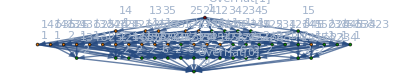

```mathematica
MobiusGraph5[K5Key,allGraphs5]
```